Intensity is proportional to |E|^2

```mathematica
FullSimplify[((1+m0 Sin[Ω t])(A1 Cos[ω0 t]+A2 Sin[ω0 t]))^2]
```

(1+m0 Sin[t Ω])^2 (A1 Cos[t ω0]+A2 Sin[t ω0])^2

```mathematica
I1 = (1 + 2 m0 Sin[Ω t]) (A1^2 Cos[ω0 t]^2+A2^2 Sin[ω0 t]^2+2 A1 A2 Cos[ω0 t]Sin[ω0 t]);
```

```mathematica
FullSimplify[((A1+A2 m0 Sin[Ω t]) Cos[ω0 t]+(A2- A1 m0 Sin[Ω t]) Sin[ω0 t])^2]
```

(Cos[t ω0] (A1+A2 m0 Sin[t Ω])+(A2-A1 m0 Sin[t Ω]) Sin[t ω0])^2

```mathematica
I2 = A1 Cos[ω0 t]^2 (A1 + 2 A2 m0 Sin[Ω t]) + A2 Sin[ω0 t]^2 (A2 - 2 A1 m0 Sin[Ω t]) + 2 Sin[ω0 t]Cos[ω0 t](A1 A2 + m0 Sin[Ω t](A2^2-A1^2)) ;
```

```mathematica
DeM = D0 Cos[Ω t + Subscript[ϕ, X]];
```

Take FT of signal times D(t) and low pass (simplified here, we just look for δ(ω) coefficient for f = 0)

```mathematica
FourierTransform[I1 DeM, t, ω]
```

-1/2 ⅈ A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω]-1/2 ⅈ A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω]+1/2 ⅈ A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω]+1/2 ⅈ A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω]+1/2 ⅈ A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω]+1/2 ⅈ A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω]+1/2 A1^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω]+1/2 A2^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω]+1/2 A1^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω]+1/2 A2^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω]-1/2 ⅈ A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω]-1/2 ⅈ A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω]-1/4 ⅈ A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/2 A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/4 ⅈ A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/4 ⅈ A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]-1/2 A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]-1/4 ⅈ A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω-2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω-2 ω0]-1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω-2 ω0]+1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω-2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω-2 ω0]-1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω-2 ω0]-1/4 ⅈ A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω-2 ω0]+1/2 A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω-2 ω0]+1/4 ⅈ A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω-2 ω0]-1/4 ⅈ A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]-1/2 A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]+1/4 ⅈ A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]+1/4 ⅈ A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]+1/2 A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]-1/4 ⅈ A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]+1/4 ⅈ A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω+2 ω0]+1/2 A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω+2 ω0]-1/4 ⅈ A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω+2 ω0]+1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω+2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω+2 ω0]-1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω+2 ω0]+1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω+2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω+2 ω0]-1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω+2 ω0]+1/4 ⅈ A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 (Ω+ω0)]-1/2 A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 (Ω+ω0)]-1/4 ⅈ A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 (Ω+ω0)]-1/4 ⅈ A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 (Ω+ω0)]-1/2 A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 (Ω+ω0)]+1/4 ⅈ A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 (Ω+ω0)]

```mathematica
- D0 m0 (π/2)^(1/2)(A1^2+A2^2)Sin[Subscript[ϕ, X]] DiracDelta[ω];
```

```mathematica
FourierTransform[I2 DeM, t, ω]
```

1/2 A1^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω]+1/2 A2^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω]+1/2 A1^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω]+1/2 A2^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω]-1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]-1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 ω0]+1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω-2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω-2 ω0]-1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω-2 ω0]+1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω-2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω-2 ω0]-1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω-2 ω0]-1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω-2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω-2 ω0]+1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 Ω-2 ω0]+1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]-1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]-1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]+1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 ω0]-1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω+2 ω0]+1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω+2 ω0]+1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 Ω+2 ω0]+1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω+2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω+2 ω0]-1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) √(π/2) DiracDelta[ω-Ω+2 ω0]+1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω+2 ω0]-1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω+2 ω0]-1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) √(π/2) DiracDelta[ω+Ω+2 ω0]+1/4 A1^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 (Ω+ω0)]+1/2 ⅈ A1 A2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 (Ω+ω0)]-1/4 A2^2 D0 ⅇ^(-ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω-2 (Ω+ω0)]+1/4 A1^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 (Ω+ω0)]-1/2 ⅈ A1 A2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 (Ω+ω0)]-1/4 A2^2 D0 ⅇ^(ⅈ ϕ_X) m0 √(π/2) DiracDelta[ω+2 (Ω+ω0)]

```mathematica
0;
```

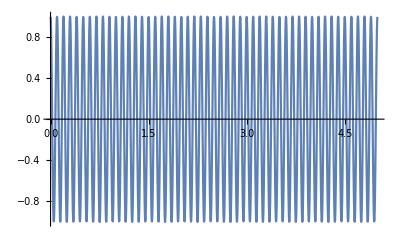

```mathematica
ω00 = 2 π 10;
m00 = 0.1;
Ω00 = 2 π;
Efield[t_] :=Cos[ω00 t] - m00 Sin[ω00 t] Sin[Ω00 t];
Plot[Efield[t],{t,0,5}]
```